## Stability analysis

```mathematica
dA[A_,J_,μ_]:= A^2-(X[J,μ]-1)^2/(4B[J] X[J,μ] + (X[J,μ]-1)^2);
```

```mathematica
sol = Solve[dA[A]==0,A]
```

{{A→-(-1+X)/(√(1-2 X+4 B X+X^2))},{A→(-1+X)/(√(1-2 X+4 B X+X^2))}}

```mathematica
ϕp = A/.sol[[1]];
ϕm = A/.sol[[2]];
```

```mathematica
phasePortrait[f_,{{xmin_,xmax_},{ymin_,ymax_}}]:=Plot[f[x],{x,xmin,xmax},Frame->True,PlotStyle->Directive[Black,Thick],ImageSize->500,PlotRange->{{xmin,xmax},{ymin,ymax}},Epilog->{getMarkers[f],getArrows[f,{xmin,xmax}]}]

right=Triangle[{{2,0},{-1,1},{-1,-1}}];
left=Triangle[{{-2,0},{1,1},{1,-1}}];
stable=Disk[];
unstable={White,Disk[],Black,Thick,Circle[]};
halfStableRight={White,Disk[],Black,Thick,Circle[],Disk[{0,0},{1,1},{-Pi/2,Pi/2}]};
halfStableLeft={White,Disk[],Black,Thick,Circle[],Disk[{0,0},{1,1},{Pi/2,3 Pi/2}]};

insetMarker[marker_,x_]:=Inset[Graphics[marker],{x,0},{0,0},Scaled[{0.05,0.05}]]

getMarkers[f_]:=Module[{x},Switch[{f[x-0.01],f[x+0.01]},{_?Positive,_?Positive},insetMarker[halfStableLeft,x],{_?Negative,_?Negative},insetMarker[halfStableRight,x],{_?Positive,_?Negative},insetMarker[stable,x],{_?Negative,_?Positive},insetMarker[unstable,x]]/.Solve[f[x]==0,x,Reals]]

getArrows[f_,{xmin_,xmax_}]:=Module[{x,sols,pos},sols=DeleteDuplicates[x/.Solve[f[x]==0,x,Reals]];
sols=Select[sols,xmin<#<xmax&];
sols=Prepend[sols,xmin];
sols=Append[sols,xmax];
pos=MovingAverage[sols,2];
If[f[#]>0,insetMarker[right,#],insetMarker[left,#]]&/@pos]
```

```mathematica
X[J_,μ_]:=Exp[J+μ];
B[J_]:= Exp[-J];
```

```mathematica
dAn[A_]:=dA[A,-2,-4]
```

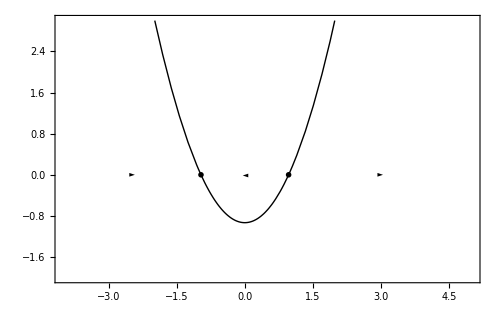

```mathematica
phasePortrait[dAn,{{-4,5},{-2,3}}]
```